## An Implementation of Quantitative Realism

## Introduction

### Context and Purpose

#### About This Project

This project implements quantitative realism, a computational theory of international relations. For more information, please see www.realpolitik.io.

#### Github Repository

The Github repository for this code is github.com/mpoulshock/QuantitativeRealism.

### Conventions

#### General

Functions that start with lower case letters are not intended to be invoked directly but instead to support other functions.

An automated regression test suite can be found at the end of this notebook.

#### Frequently Used Objects

s - size vector
T - tactic matrix
TT - ternary tactic matrix
tactic - tactic vector
i - index of a given agent

#### Color Coding

Initialization cells are highlighted in gray.

Alternate implementations are highlighted in blue.

Examples are highlighted in orange.

Unit tests are highlighted in brown.

Warnings are highlighted in red.

### License

TBD

## Data Structures

### Parameters

#### Get and Set

Global variables can be called by other functions without having them passed in as arguments. This function provides a way to set global parameters from an Association. Output: none.

```mathematica
SetParameters[p_Association]:= Block[{},
β=N[Lookup[p,"β",β]]; (* Constructive power multiplier *)
μ=N[Lookup[p,"μ",μ]]; (* Destructive power multiplier *)
λ=N[Lookup[p,"λ",λ]]; (* Rate of power decay *)
α=N[Lookup[p,"α",α]]; (* Utility function exponent *)
δ=N[Lookup[p,"δ",0.85]]; (* Discount rate *)
ρ=N[Lookup[p,"ρ",ρ]]; (* Minimum self-allocation percentage *)
k=Lookup[p,"k",10]; (* Steps used in PrinceRank simulations *)
discountFactors=(1-δ)*Table[δ^i,{i,k}];
]
```

Set the global parameters. Output: none.

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.25, "ρ"->0.98|>];
```

A version that overrides default parameters. Output: none.

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.25,"δ"->0.85, "ρ"->0.98,"k"->10|>];
```

Assembles global parameters into an Association. Output: Association.

```mathematica
GetParameters:= <|"β"-> β,"μ"-> μ,"λ"-> λ,"α"-> α,"δ"-> δ,"ρ"-> ρ,"k"->k|>
```

Generate a string showing the parameters. Output: string.

```mathematica
ParameterString:=Caption[
"β="<>ToString[β]<>", μ="<>ToString[μ]<>", λ="<>ToString[λ]<>", α="<>ToString[α]<>", ρ="<>ToString[ρ]<>", δ="<>ToString[δ]];
```

#### Num

Determine the number of agents in a power structure. Beware of performance impact if this is used in a repetitive operation. Output: integer.

```mathematica
Num[ps_Association]:=Length[ps["s"]];
Num[T_List]:=Length[T];
```

#### Discount rate (δ)

Discount rate error threshold (5%).

```mathematica
discountErrorThreshold = 0.05;
```

Given the discount rate δ, returns the number of future steps required. Output: integer.

```mathematica
DeltaToSteps[δ_Real]:=Ceiling[Log[δ,discountErrorThreshold]]
```

```mathematica
DeltaToSteps[δ_Real]:=DeltaToSteps[δ]=Ceiling[Log[δ,discountErrorThreshold]]
```

Given a number of steps, returns the value of δ that would require those steps. Output: real number.

```mathematica
StepsToDelta[steps_Integer]:= Surd[discountErrorThreshold,steps]
```

### Power Structures

#### PowerStructure

A power structure is represented as an Association composed of a size vector (s) and a tactic matrix (T). The following functions instantiate power structures. They should be avoided when performance matters.

```mathematica
<|"s"->{4.3,4.2},"T"->{{0.5,0.5},{-0.5,0.5}}|>
```

Creates a new power structure object. If the tactic matrix is ternary, it gets legalized. Output: power structure.

```mathematica
PowerStructure[s_List,T_List?TernaryMatrixQ]:= PowerStructure[s,NormalizeTernaryT[T]]
```

Creates a new power structure object. This is the base function. Output: power structure.

```mathematica
PowerStructure[s_List,T_List?MatrixQ]:= <|"s"->N[s],"T"->N[T]|>
```

Creates a new power structure from only a tactic matrix. If the tactic matrix is ternary, it gets legalized. The size vector is a list of 1s. Output: power structure.

```mathematica
PowerStructure[TT_List?TernaryMatrixQ]:= PowerStructure[NormalizeTernaryT[TT]]
```

Same as the above, but it does not alter the tactic matrix.

```mathematica
PowerStructure[T_List?MatrixQ]:= PowerStructure[Table[1.,Length[T]],T]
```

#### PowerStructureR

Instantiate a power structure in which the ternary tactic matrix is reciprocalized. Output: power structure.

```mathematica
PowerStructureR[s_,TT_]:=PowerStructure[s,ReciprocalizeT[s,TT]]
```

#### RandomPowerStructure

Generate a random power structure, specifying the number of nodes (n). By convention, the size vector in the first state of a simulation is normalized. Output: power structure.

```mathematica
RandomPowerStructure[n_Integer]:= PowerStructure[RandomS[n],RandomT[n]]
```

#### RandomS

Creates a random size vector for n agents, normalized to unity. Output: size vector.

```mathematica
RandomS[n_Integer]:= NormalizeS[RandomReal[{0,1},n]]
```

Unit tests:

```mathematica
unitTests["RandomS"] :={
VerificationTest[
Max[RandomS[5]],
1.,
TestID->"RandomS1"
]
};
```

#### RandomTernaryPowerStructure

Generate a random power structure, of size n, with symmetric ternary edges and small-world connectivity. Output: power structure.

```mathematica
RandomTernaryPowerStructure[n_Integer]:=RandomTernaryPowerStructure[n,2n,0.1]
```

```mathematica
RandomTernaryPowerStructure[n_Integer,edges_Integer,negativity_Real]:=PowerStructure[RandomS[n],NormalizeTernaryT[RandomTernaryT[n,edges,negativity]]]
```

#### AddAlphaList

Adds a α vector as an attribute of a power structure. Output: power structure.

```mathematica
AddAlphaList[ps_Association,α_List]:=Join[ps,<|"α"->α|>]
```

#### Pretty

Displays a power structure with rounded values and components shown in MatrixForm. Output: a power structure.

```mathematica
Pretty[ps_Association]:= Map[MatrixForm[PrettyRound[#,.001]]&,ps]
PrettyRound[x_,n_]:=DeDecimalize[Round[x,n]];
PrettyRound[x_List?TernaryMatrixQ,n_]:=DeDecimalize[x];
```

```mathematica
Pretty[RandomPowerStructure[3]]
```

<|s→(0.581
0.493
1.),T→(0.906 | -0.029 | -0.021
-0.073 | 0.959 | -0.029
0.021 | 0.013 | 0.95)|>

A version that can be called on a tactic matrix. Output: a tactic matrix.

```mathematica
Pretty[T_List?MatrixQ]:=MatrixForm[PrettyRound[T,.001]]
```

## Helper Functions

### Scalar

#### DeDecimalize

Removes extraneous decimal points from integers. Output: number.

```mathematica
DeDecimalize[n_]:=If[n==IntegerPart[n],IntegerPart[n],n]
```

### List

#### PositionLargest

Gives the position of the first element that has the largest value in list. Stolen from: https://resources.wolframcloud.com/FunctionRepository/resources/PositionLargest.  Output: list of integers.

```mathematica
PositionLargest[list_List]/;AllTrue[list,NumericQ]:=First[FirstPosition[list,Max[list]]]
```

```mathematica
PositionLargest[list_List,n_Integer]/;AllTrue[list,NumericQ]:=Take[Flatten[Position[list,#]&/@DeleteDuplicates[TakeLargest[list,n]]],n]
```

```mathematica
PositionLargest[list_List,HoldPattern[UpTo][n_Integer]]/;AllTrue[list,NumericQ]:=Take[Flatten[Position[list,#]&/@DeleteDuplicates[TakeLargest[list,UpTo[n]]]],UpTo[n]]
```

#### RandomPosition

Gives a random position at which objects matching pattern appear in expr.

```mathematica
RandomPosition[expr_,pattern_]:= RandomChoice[Flatten[Position[expr,pattern]]]
```

```mathematica
RandomPosition[{a,a,b,a,c,b},b]
```

5

### Matrix

#### MapTransposed

Maps a function down the columns of a matrix. Output: matrix.

```mathematica
MapTransposed[f_,M_List?MatrixQ]:= Transpose[Map[f,Transpose[M]]];
SetAttributes[MapTransposed,HoldFirst];
```

#### ReplaceColumn

Replace a column in a matrix M with a given list. Output: matrix.

```mathematica
ReplaceColumn[M_List,i_Integer,list_List]:=Block[{m=M},
m[[All,i]]=list;
Return[m];
]
```

#### ReplaceDiagonal

Replaces the diagonal of a matrix with a given list.  This implementation is ugly but fast. Output: matrix. NOTE: This is not used anywhere.

```mathematica
ReplaceDiagonal[M_List?MatrixQ,diag_List] := M - DiagonalMatrix[Diagonal[M]] + DiagonalMatrix[diag]
```

A faster version to use when all input elements are known to be reals.

```mathematica
ReplaceDiagonalReals=FunctionCompile[Function[{
Typed[M,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[diag,TypeSpecifier["PackedArray"]["Real64",1]]
},Block[{R=M,i,m=Length[M]},
For[i=1,i≤m,i++,  
R[[i,i]] = diag[[i]];
]; 
Return[R];
]]];
```

#### ZeroDiagonalize

Overwrites the diagonal of a matrix with all zeroes. Every element in the matrix is assumed to be a Real. Output: a matrix.

```mathematica
ZeroDiagonalize[M_List]:=ReplaceDiagonalReals[M,Table[0.,Length[M]]]
```

#### ZeroMatrix

Creates a matrix of all zeroes, of a given dimension. Output: matrix.

```mathematica
ZeroMatrix[n_]:=Table[0,{i,n},{j,n}]
```

```mathematica
ZeroMatrix[4]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Unit tests

Unit tests for the helper functions:

```mathematica
unitTests["HelperFunctions"]:={
VerificationTest[
MapTransposed[Differences,IdentityMatrix[4]],
{{-1,1,0,0},{0,-1,1,0},{0,0,-1,1}},
TestID->"HelperFunctions_MapTransposed1"
],
VerificationTest[
ReplaceColumn[IdentityMatrix[3],1,{5,6,7}],
{{5,0,0},{6,1,0},{7,0,1}},
TestID->"HelperFunctions_ReplaceColumn1"
],
VerificationTest[
ReplaceDiagonalReals[N[IdentityMatrix[3]],N[{9,10,11}]],
N[{{9,0,0},{0,10,0},{0,0,11}}],
TestID->"HelperFunctions_ReplaceDiagonal1"
],
VerificationTest[
PositionLargest[{100,200,100,200,50}],
2,
TestID->"HelperFunctions_PositionLargest1"
],
VerificationTest[
PositionLargest[{100,200,100,200,50},1],
{2},
TestID->"HelperFunctions_PositionLargest2"
],
VerificationTest[
PositionLargest[{100,200,100,200,50},3],
{2,4,1},
TestID->"HelperFunctions_PositionLargest3"
],
VerificationTest[
ZeroDiagonalize[N[{{2,6,8},{5,9,6},{6,6,2}}]],
N[{{0,6,8},{5,0,6},{6,6,0}}],
TestID->"HelperFunctions_ZeroDiagonalize1"
]
};
```

## Tactics

### Type testing

#### LegalTacticQ

Determines whether a tactic vector is legal, in the sense that the total of the absolute values of all tactics is 1. Output: Boolean.

```mathematica
LegalTacticQ[tactic_List] := Total[Abs[tactic]]==1;
```

Unit tests:

```mathematica
unitTests["LegalTacticQ"] :={
VerificationTest[
LegalTacticQ[{.5,0,0,-.5}],
True,
TestID->"LegalTacticQ1"
],
VerificationTest[
LegalTacticQ[{.5,.2,0,-.5}],
False,
TestID->"LegalTacticQ2"
]
};
```

#### LegalTQ

Determines whether a tactic matrix is legal (see above). Output: Boolean.

```mathematica
LegalTQ[T_List?MatrixQ]:= AllTrue[Map[LegalTacticQ,Transpose[T]],TrueQ];
```

Unit tests:

```mathematica
unitTests["LegalTQ"] :={
VerificationTest[
LegalTQ[({{0.5, 0.3}, {-0.5, 0.7}})],
True,
TestID->"LegalTQ1"
],
VerificationTest[
LegalTQ[({{0.6, 0.3}, {-0.5, 0.7}})],
False,
TestID->"LegalTQ2"
]
};
```

#### TernaryMatrixQ

Determines whether a matrix is a ternary matrix (i.e. one composed only of -1, 0, or 1s). Output: Boolean.

```mathematica
TernaryMatrixQ[TT_List?MatrixQ]:= ContainsOnly[Flatten[TT],{-1.,0.,1.}]
```

Unit tests:

```mathematica
unitTests["TernaryMatrixQ"] :={
VerificationTest[
TernaryMatrixQ[N[IdentityMatrix[3]]],
True,
TestID->"TernaryMatrixQ1"
],
VerificationTest[
TernaryMatrixQ[RandomReal[{0,1},{3,3}]],
False,
TestID->"TernaryMatrixQ2"
]
};
```

### Normalization

#### NormalizeS

Normalizes the size vector so that all sizes are between 0 and 1.  The largest agent always ends up with a size of 1. This is slightly faster than an equivalent complied version. Output: size vector.

```mathematica
NormalizeS[s_List] := Block[{max=Max[s]},
N[If[max==0,s,s/max]]
]
```

A version that works on power structures. Output: power structure.

```mathematica
NormalizeS[ps_Association]:=Block[{r=ps},
AssociateTo[r,"s"->NormalizeS[ps["s"]]];
Return[r];
]
```

Unit tests:

```mathematica
unitTests["NormalizeS"] :={
VerificationTest[
NormalizeS[{0,0,0}],
{0.,0.,0.},
TestID->"NormalizeS1"
],
VerificationTest[
NormalizeS[{.5,.3,0}],
{1.,0.6,0.},
TestID->"NormalizeS2"
],
VerificationTest[
NormalizeS[{5,13,0.3}],
{0.38461538461538464,1.,0.023076923076923078},
TestID->"NormalizeS3"
]
};
```

#### NormalizeTactic

Given a random tactic vector, this function adjusts its length so as to make it a legal tactic.  A legal tactic is a point on the surface of a cross-polytope whose dimension is equal to the number of agents. Note: A zero vector 0 will remain 0. Output: tactic vector.

```mathematica
NormalizeTactic[list_List]:=NormalizeTacticCompiled[N[list]]
```

```mathematica
NormalizeTacticCompiled=FunctionCompile[Function[{
Typed[list,TypeSpecifier["PackedArray"]["Real64",1]]
},Block[{tot=Total[Abs[list]]},If[tot==0,list,list / tot]]
]];
```

Unit tests:

```mathematica
unitTests["NormalizeTactic"] :={
VerificationTest[
NormalizeTactic[{0.1,0,0}],
{1.,0.,0.},
TestID->"NormalizeTactic1"
],
VerificationTest[
NormalizeTactic[{0,0,0}],
{0.,0.,0.},
TestID->"NormalizeTactic2"
],
VerificationTest[
NormalizeTactic[{1,2,4,4.}],
{0.09090909090909091,0.18181818181818182,0.36363636363636365,0.36363636363636365},
TestID->"NormalizeTactic3"
],
VerificationTest[
NormalizeTactic[{-1,0,0,1}],
{-0.5,0.,0.,0.5},
TestID->"NormalizeTactic2"
]
};
```

#### NormalizeT

Output: a normalized tactic matrix.

```mathematica
NormalizeT[T_List?MatrixQ]:=MapTransposed[NormalizeTactic,T]
```

#### NormalizeTernaryT

Legalizes a ternary matrix, which is a different algorithm because ρ has to be inserted for the self-allocations. Note: the self-allocation will always be ρ, even if all other allocations are 0. Output: tactic matrix.

```mathematica
NormalizeTernaryT[TT_List] :=ReplaceDiagonalReals[Transpose[Transpose[TT]/ReplaceAll[N[Total[Abs[TT]]], 0.->1.]]*(1.-ρ),Table[ρ,Length[TT]]]
```

A version that sets ρ to 1 when all other allocations are 0:

```mathematica
NormalizeTernaryT[TT_List] :=Block[{x,t=N[Total[Abs[TT]]]},
x=Transpose[Transpose[TT]/ReplaceAll[t, 0.->1.]]*(1.-ρ);
ReplaceDiagonalReals[x,Map[If[#==0.,1.,ρ]&,t]]
]
```

Unit tests:

```mathematica
unitTests["NormalizeTernaryT"] :={
VerificationTest[
NormalizeTernaryT[{{0,1},{-1,0}}],
{{0.9,0.09999999999999998},{-0.09999999999999998,0.9}},
TestID->"NormalizeTernaryT1"
]
};
```

#### NormalizeTernaryTactic

Given a ternary tactic vector, convert it to a legal tactic vector. The focal agent gets a preset self-allocation, and all of the outgoing allocations are apportioned accordingly. Self-allocations on the input tactic are ignored. Output: tactic vector.

Compile this (same pattern as FixSelfAllocation)

```mathematica
NormalizeTernaryTactic[tactic_List,i_Integer]:= ReplacePart[NormalizeTacticCompiled[tactic] * (1.-ρ),i->ρ]
```

#### InsertSelfAllocation

Given a tactic vector, set the self-allocation percentage ρ of agent i such that the result is a legal tactic vector. It is assumed that the self-allocation amount in the input tactic vector is 0. Output: tactic vector.

```mathematica
InsertSelfAllocation[tactic_,i_]:= ReplacePart[tactic,i->1-Total[Abs[tactic]]]
```

```mathematica
InsertSelfAllocation[{0,0.035,0,-0.009,0},1]
```

{0.956,0.035,0,-0.009,0}

Applies the function above to a tactic matrix. Output: tactic matrix.

```mathematica
InsertSelfAllocation[T_]:=Transpose[MapIndexed[InsertSelfAllocation[#,First[#2]]&,Transpose[T]]]
```

```mathematica
InsertSelfAllocation[({{0, -.005, 0}, {.02, 0, 0}, {.01, 0, 0}})]//Pretty
```

(0.97 | -0.005 | 0.
0.02 | 0.995 | 0.
0.01 | 0. | 1.)

#### GravitizeTernaryT

Given a ternary tactic matrix, adjust the allocations to make them proportional to the sizes of the agents. The resulting allocations will be akin to a gravity model of trade. Output: tactic matrix.

```mathematica
GravitizeTernaryT[TT_,s_]:=NormalizeTernaryT[s*TT]
```

A second form of gravitization gives each relationship a fixed amount of potential power that’s proportional to the other agents’ sizes. The tactic vector is then normalized by allocating all unused power back to each agent. Output: tactic vector.

```mathematica
GravitizeTernaryTactic[tactic_,s_,i_]:=InsertSelfAllocation[tactic*s*(1-ρ)/Total[s],i]
```

Applies the second form of gravitization to a tactic matrix. Output: tactic matrix.

```mathematica
GravitizeTernaryT[TT_,s_]:=Transpose[MapIndexed[GravitizeTernaryTactic[#,s,First[#2]]&,Transpose[TT]]]
```

### Continuous Tactics

#### RandomTactic

Generates a random tactic vector. Note that this may entail self-harm. Output: tactic vector.

```mathematica
RandomTactic[n_Integer]:=NormalizeTactic[RandomPoint[Sphere[Table[0,n]]]]
```

Generates a random tactic vector in which a specified agent is not harming itself. The allocation to the focal agent is at least ρ. Output: tactic vector.

```mathematica
RandomTactic[n_Integer,index_Integer]:=With[{a=RandomReal[{ρ,1}]},
Insert[(1-a)RandomTactic[n-1],a,index]
]
```

Unit tests:

```mathematica
unitTests["RandomTactic"] :={
VerificationTest[
LegalTacticQ[RandomTactic[5]],
True,
TestID->"RandomTacticVector1"
],
VerificationTest[
First[RandomTactic[5,1]]>0,
True,
TestID->"RandomTacticVector2"
]
};
```

#### RandomT

Generates a random tactic matrix for n agents. Output: tactic matrix.

```mathematica
RandomT[n_Integer] :=Transpose[Table[RandomTactic[n,i],{i,n}]]
```

Unit tests:

```mathematica
unitTests["RandomTacticMatrix"] :={
VerificationTest[
LegalTQ[RandomT[3]],
True,
TestID->"RandomTacticMatrix1"
]
};
```

#### RandomTNear

Given a tactic matrix, randomly alter agent i’s tactic with respect to another randomly selected agent j. The resulting tactic is symmetrical (reciprocal) in the sense that T_ijand T_jihave the same polarity, even if they vary in intensity. Only one relationship is altered. Output: tactic matrix.

```mathematica
RandomTNear[T_,i_]:=Block[{j,ti,tj},
j=RandomChoice[Delete[Range[Length[T]],i]]; 
{ti,tj}=RandomReal[{0,RandomChoice[{1,-1}]*(1.-ρ)},2];
ReplaceColumn[ReplaceColumn[T,i,NormalizeTernaryTactic[ReplacePart[T[[All,i]],{j->tj,i->0.}],i]],j,NormalizeTernaryTactic[ReplacePart[T[[All,j]],{i->ti,j->0.}],j]]
]
```

#### RandomTacticNear

Given a tactic vector, this function finds another tactic (approximately) within a given Euclidean distance σ. It is assumed that agents do not harm themselves. The new tactic is found by: (1) starting from a point represented by the original tactic, (2) picking a random point on a sphere of radius σ, centered at the original point, (3) ensuring that the self-allocation is nonnegative, and (4) normalizing the point on the sphere back to the surface of the n-dimensional cross-polytope. Output: tactic vector.

```mathematica
RandomTacticNear[tactic_List, index_Integer, σ_Real] := NormalizeTactic[MapAt[Abs,RandomPoint[Sphere[tactic,σ]],index]]
```

### Ternary Tactics

#### Focal Agent Symmetric Triads

Generate a symmetrical tactic matrix from a tuple of {-1, 0, 1}’s.

```mathematica
GenerateSymmetricTernaryTacticMatrix[{a_,b_,c_}]:=({{0, a, c}, {a, 0, b}, {c, b, 0}})
```

Remove tuples that are symmetrical from agent #1’s perspective.

```mathematica
FocalAgentSymmetricTriads = Map[GenerateSymmetricTernaryTacticMatrix,{{-1,-1,-1},{-1,-1,0},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,1,-1},{-1,1,0},{-1,1,1},{0,-1,0},{1,-1,0},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,-1,-1},{1,-1,1},{1,0,1},{1,1,1}}];
```

#### MovesNear

Given a power structure, find nearby ternary moves (not necessarily symmetric) which apply the law of motion. Nearness is assumed to be dx=1. Output: list of power structures.

```mathematica
MovesNear[ps_Association,i_Integer]:=Block[{s=ps["s"],T=ps["T"]},
Map[UpdatePowerStructure[PowerStructure[s,NormalizeTernaryT[#]]]&,TernaryTsNear[ToTernary[T],i,1]]]
```

```mathematica
ps=PowerStructure[{1.,1.,1.},Symmetric3s[[21]]];
MovesNear[ps,1]
```

{<|s→{0.85,0.85,0.85},T→{{0.9,0.05,-0.05},{-0.05,0.9,0.05},{-0.05,0.05,0.9}}|>,<|s→{0.85,1.,0.7},T→{{0.9,0.05,-0.05},{0.,0.9,0.05},{-0.1,0.05,0.9}}|>,<|s→{0.85,1.1,0.85},T→{{0.9,0.05,-0.05},{0.05,0.9,0.05},{-0.05,0.05,0.9}}|>,<|s→{0.85,1.2,1.},T→{{0.9,0.05,-0.05},{0.1,0.9,0.05},{0.,0.05,0.9}}|>,<|s→{0.85,1.1,1.1},T→{{0.9,0.05,-0.05},{0.05,0.9,0.05},{0.05,0.05,0.9}}|>}

#### NotateMove

Given two power structures and an agent i, indicate i’s move in ternary notation form. In a given pair, agent i is listed first. Output: list of pair-tactic rules.

```mathematica
NotateMove[before_Association,after_Association,i_Integer]:=Block[{b,a},
b=ToTernary[before["T"]][[All,i]];
a=ToTernary[after["T"]][[All,i]];
Map[{i,#} ->a[[#]]&,Flatten[Position[b-a,_?(#≠0&)]]]
]
```

```mathematica
NotateMove[PowerStructure[({{0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, -1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}})],PowerStructure[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, -1, 0, 0, 0}, {0, 0, 0, 0, 0}})],2]
```

{{2,1}→0.,{2,3}→1.,{2,4}→-1.}

Detect a move, assumed to be symmetric, by a given agent, and return it in notation form. Null moves are returned as Nothing. Output: {pair->tactic, reversePair->tactic}.

```mathematica
NotateSymmetricMove[ps1_, ps2_, i_]:=Block[{move=NotateMove[ps1,ps2,i]},
If[move=={},Nothing,{move[[1]],Reverse[move[[1,1]]]->move[[1,2]]}]
]
```

#### RandomSimultaneousMoveNear

For a given power structure, generate a random move near it, assuming that all agents move simultaneously by altering no more than a single relationship. After the agents’ random moves have been selected, the tactic matrix is symmetrized. Output: a power structure.

```mathematica
RandomSimultaneousMoveNear[ps_]:=Block[{T,s=ps["s"]},
T=ReciprocalizeT[s,RandomTernaryTNear[ps["T"]]];
Association["s"->UpdateS[s,T],"T"->T]
]
```

A version that appends M, a move matrix (“M”) appended indicating the ternary tactic each agent played before symmetrization:

```mathematica
RandomSimultaneousMoveNear[ps_]:=Block[{M,T,s=ps["s"]},
M=RandomTernaryTNear[ps["T"]];
T=ReciprocalizeT[s,M];
Association["s"->UpdateS[s,T],"T"->T,"M"->M]
]
```

```mathematica
Pretty[RandomSimultaneousMoveNear[ps]]
```

<|s→(0.092
0.987
0.703
0.255
0.329),T→(0.98 | 0.001 | -0.001 | -0.002 | -0.007
0.002 | 0.998 | 0. | -0.005 | 0.
-0.002 | 0. | 0.991 | 0.005 | -0.01
-0.002 | -0.001 | 0.002 | 0.983 | 0.003
-0.014 | 0. | -0.007 | 0.005 | 0.98)|>

#### RandomTernaryT

Generate a random symmetric ternary tactic matrix of size n, with a given number of edges, some percentage of which are negative. This function piggybacks on RandomGraph to generate a small-world graph with a given number of nodes and edges. Output: tactic matrix.

```mathematica
RandomTernaryT[n_Integer]:=RandomTernaryT[n,2n,0.1]
```

```mathematica
RandomTernaryT[n_Integer,edges_Integer,negativity_Real]:=Block[{T,g=RandomGraph[{n,edges}]},
T=Normal[SparseArray[Map[#[[1]]-> RandomChoice[{negativity,1-negativity}-> {-1.,1.}]&,Drop[ArrayRules[UpperTriangularize[AdjacencyMatrix[g]]],-1]],{n,n}]];
N[T+Transpose[T]]
]
```

#### RandomTernaryTNear

Given a (non-ternary) tactic matrix, return a ternary tactic matrix in which each agent alters a single relationship. Output: ternary tactic matrix.

```mathematica
RandomTernaryTNear=FunctionCompile[Function[{
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]]
},Block[{R=Sign[T],i,m=Length[T]},
For[i=1,i≤m,i++, 
R[[RandomInteger[{1,m}],i]]=RandomInteger[{-1,1}];
R[[i,i]] =0;
]; 
Return[N[R]];
]]];
```

```mathematica
RandomTernaryTNear[ps["T"]]//Pretty
```

(0 | 1 | -1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

#### ReciprocalizeT

Given a move matrix M, return a tactic matrix such that for each pair of agents, the relationship is made reciprocal to the more negative of the two transfers of power. The amount transferred is based on the percentage of power allocated times the size of the allocating agent. The motivation for this function is to try to equalize the amount of flow between any two agents. Note that perfect reciprocity is often not achieved due to size differences. Output: tactic matrix.

Processing steps:
(a) Transpose, normalize the ternary T, and multiply it by s;
(b) Symmetrize the T;
(c) Divide the T by s;
(d) Fix the self-allocations and transpose back;

```mathematica
ReciprocalizeT[s_,M_]:=Transpose[MapIndexed[FixSelfAllocation[#,First[#2],ρ]&,ReciprocalizeTCompiled[s,M,ρ]]]
```

```mathematica
ReciprocalizeTCompiled=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[M,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[ρ,TypeSpecifier["Real64"]]
},Block[{a,b,c,d},
a=(1.-ρ)Map[Block[{t=Total[Abs[#]]},If[t==0,#,# / t]]&,Transpose[M]]*s;
b=a-Ramp[a-Transpose[a]];
c=MapIndexed[If[s[[First[#2]]]==0.,#,#/s[[First[#2]]]]&,b];
Return[c]
]]];
```

If total > 1-ρ, normalize; else, insert self-allocation. Assumes that the self-allocated amount is 0. Output: tactic vector.

```mathematica
FixSelfAllocation=FunctionCompile[Function[{
Typed[tactic,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[i,TypeSpecifier["MachineInteger"]],
Typed[ρ,TypeSpecifier["Real64"]]
},Block[{t=Total[Abs[tactic]],r=tactic},
If[t≤ 1.-ρ,r[[i]]=1.-t,r=r / t * (1.-ρ);r[[i]]=ρ;];
Return[r];
]
]];
```

```mathematica
ρ=.9;ReciprocalizeT[{1.,.3,.2,.4},N[({{0, 1, 1, 1}, {1, 0, 0, 0}, {1, -1, 0, 0}, {1, 0, 0, 0}})]]//Pretty
```

(0.932 | 0.05 | 0.057 | 0.083
0.015 | 0.9 | -0.043 | 0.
0.02 | -0.05 | 0.9 | 0.
0.033 | 0. | 0. | 0.917)

#### SymmetricMovesNear

Given a power structure, find nearby symmetric ternary moves which apply the law of motion. Nearness is assumed to be dx=1. Output: list of power structures.

```mathematica
SymmetricMovesNear[ps_Association,i_Integer]:=Map[Join[#,<|"pr"->PrinceRank[#]|>]&,Map[<|"s"-> UpdateS[ps["s"],#],"T"-> #|>&,SymmetricTsNear[ps["T"],i]]]
```

#### SymmetricTsNear

Given a normalized tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible symmetric tactic matrices at a distance of one changed ternary tactic. Output: list of normalized tactic matrices

```mathematica
SymmetricTsNear[T_List,i_Integer]:=With[{TT=ToTernary[T]},
Join[{T},Map[NormalizeTernaryT[ReplacePart[TT,#]]&,Flatten[Delete[Table[
If[TT[[i,j]]≠t,{{i,j}->t,{j,i}->t},Nothing]
,{j,Length[T]},{t,-1.,1.}],i],1]]]
]
```

```mathematica
MatrixForm/@SymmetricTsNear[NormalizeTernaryT[ZeroMatrix[3]],3]
```

{(0.9 | 0. | 0.
0. | 0.9 | 0.
0. | 0. | 0.9),(0.9 | 0. | -0.1
0. | 0.9 | 0.
-0.1 | 0. | 0.9),(0.9 | 0. | 0.1
0. | 0.9 | 0.
0.1 | 0. | 0.9),(0.9 | 0. | 0.
0. | 0.9 | -0.1
0. | -0.1 | 0.9),(0.9 | 0. | 0.
0. | 0.9 | 0.1
0. | 0.1 | 0.9)}

Given a ternary tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible symmetric tactic matrices within a given (Hamming) distance. Output: list of ternary tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer,dx_Integer]:=Map[ReplacePart[ReplaceColumn[T,i,#],i->#]&,TernaryTacticsNear[T,i,dx]]
```

Same as the above, but assumes that dx=1. Output: list of ternary tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer]:=Map[ReplacePart[ReplaceColumn[T,i,#],i->#]&,TernaryTacticsNear[T[[All,i]],i]]
```

A version that returns random continuous tactics. Not an efficient implementation, as ideally I would restructure how Minimax explores moves, but good enough for determining whether continuous tactics are viable. Output: list of tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer]:=Join[{T},Table[RandomTNear[T,i],20]]
```

#### SymmetrizePowerStructure

Given a power structure, convert it the tactic matrix to ternary, symmetrize it, and convert it back to a power structure. Output: power structure.

```mathematica
SymmetrizePowerStructure[ps_Association]:=PowerStructure[ps["s"],NormalizeTernaryT[SymmetrizeT[ToTernary[ps["T"]]]]]
```

#### SymmetrizeT

Given an asymmetric ternary tactic matrix that reflects each agents’ desired move, find T where the applicable relationship is the minimum of each set of pairwise moves.

Rename: SymmetrizeTernaryT?

```mathematica
SymmetrizeT=FunctionCompile[Function[{
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]]
},T-Ramp[T-Transpose[T]]
]];
```

An alternate, non-compiled version (8x slower).

```mathematica
SymmetrizeT[T_List]:=MapThread[Min,{T,Transpose[T]},2]
```

```mathematica
SymmetrizeT[N[({{0, 1, 0, -1}, {1, 0, 0, 1}, {1, 0, 0, 0}, {0, -1, 0, 0}})]] // MatrixForm
```

(0. | 1. | 0. | -1.
1. | 0. | 0. | -1.
0. | 0. | 0. | 0.
-1. | -1. | 0. | 0.)

#### TernaryTacticNearByIndex

Generate the tactic associated with the selected integer, where index is the number of the tactic that’s output from TernaryTacticsNear. Output: ternary tactic.

Consider compiling.

```mathematica
TernaryTacticNearByIndex[tactic_,i_,index_]:= If[index==1,tactic,
Block[{k=Floor[index/2.],r=tactic},
If[i≤ k,k++];
r[[k]]=DeleteCases[{-1.,0.,1.},tactic[[k]]][[Mod[index,2]+1]];
Return[r];
]]
```

#### TernaryTacticsNear

Given a ternary tactic matrix and an agent index i, list all possible tactic vectors in which a single move is altered, within a given Hamming distance. This function will also return the original tactic. Output: a list of ternary tactic vectors.

```mathematica
TernaryTacticsNear[T_List,i_Integer,dx_Integer]:=DeleteDuplicates[Flatten[Map[Tuples[ReplacePart[Partition[T[[All,i]],1],Map[#->{-1.,0.,1.}&,#]]]&,Subsets[Delete[Range[Length[T]],i],{dx}]],1]]
```

A variant for when dx=1. The input tactic is always the first item in the output list. Output: a list of ternary tactic vectors.

```mathematica
TernaryTacticsNear[tactic_List,i_Integer]:=DeleteDuplicates[Join[{tactic},Flatten[
Table[If[j==i,Nothing,{ReplacePart[tactic,j-> -1.],ReplacePart[tactic,j-> 0.],ReplacePart[tactic,j-> 1.]}],{j,Length[tactic]}],1]]]
```

```mathematica
TernaryTacticsNear[{1.,1.,1.},3]
```

{{1.,1.,1.},{-1.,1.,1.},{0.,1.,1.},{1.,-1.,1.},{1.,0.,1.}}

#### TernaryTsNear

Given a ternary tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible tactic matrices (not necessarily symmetric) within a given (Hamming) distance. Output: list of ternary tactic matrices.

```mathematica
TernaryTsNear[TT_List,i_Integer,dx_Integer]:=Map[ReplaceColumn[TT,i,#]&,TernaryTacticsNear[TT,i,dx]]
```

```mathematica
MatrixForm/@TernaryTsNear[N[IdentityMatrix[3]],2,1]
```

{(1. | -1. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 1. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | -1. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | 1. | 1.)}

#### ToTernary

Converts a legal tactic matrix to a ternary one. Output: tactic matrix.

```mathematica
ToTernary=FunctionCompile[Function[{
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]]
},Block[{R=Sign[T],i,m=Length[T]},
For[i=1,i≤m,i++,  
R[[i,i]] =0;
]; 
Return[N[R]];
]]];
```

An uncompiled version that’s ~10x slower.

```mathematica
ToTernary[T_List]:=ReplaceDiagonalReals[N[Sign[T]],Table[0.,Length[T]]]
```

Convert the tactic matrix within a power structure to ternary. Output: power structure.

```mathematica
ToTernary[ps_Association]:= <|"s"->ps["s"],"T"-> ToTernary[ps["T"]]|>
```

Unit tests:

```mathematica
unitTests["ToTernary"] :={
VerificationTest[
ToTernary[{{0.47593052648072004,0.38946778511397906,0.5887854695349517},{0.36321528609957204,0.1477143527714231,-0.3520164533294082},{0.16085418741970775,0.4628178621145978,0.05919807713564013}}],
{{0.,1.,1.},{1.,0.,-1.},{1.,1.,0.}},
TestID->"ToTernary1"
]
};
```

### Named Ts

#### NamedTHierarchy

A tactic matrix of variable size representing a hierarchy. Output: tactic matrix.

```mathematica
NamedTHierarchy[n_]:=NormalizeTernaryT[ReplacePart[ReplaceColumn[ReplacePart[ZeroMatrix[n],1-> Table[1.,n]],1,Table[1.,n]],{1,1}->0.]]
```

#### NamedTComplete

A tactic matrix of variable size representing a fully connected graph. Output: tactic matrix.

```mathematica
NamedTComplete[n_]:=NormalizeTernaryT[ReplaceDiagonalReals[Table[1.,{i,n},{j,n}],Table[0.,n]]]
```

#### NamedTNull

```mathematica
NamedTNull[n_]:=NormalizeTernaryT[ZeroMatrix[n]]
```

### Pad/Trim

#### PadPowerStructure

Given a scenario, these functions reduce it to a smaller n (if possible) or pad it to a larger n (if necessary). Convert a scenario with a lower n to a higher n. So, for example, a scenario could be defined in n=3 but be run against a neural net of size n=5. Output: power structure.

```mathematica
PadPowerStructure[ps_Association,n_Integer]:= PowerStructure[PadS[ps["s"], n],PadT[ps["T"],n]]
```

Pads a size vector. Output: size vector.

```mathematica
PadS[s_, n_] := PadRight[s,n,0.];
```

Unit tests:

```mathematica
unitTests["PadSizeVector"]:={
VerificationTest[
PadS[{1,1,0.3},5],
{1,1,0.3,0,0},
TestID->"PadSizeVector1"
]
};
```

Pads a tactic matrix. Output: tactic matrix.

```mathematica
PadT[T_,n_]:=With[{pad=n-Length[T]},
ArrayPad[T,{{0,pad},{0,pad}},0.]
]
```

Unit tests:

```mathematica
unitTests["PadTacticMatrix"]:={
VerificationTest[
PadT[IdentityMatrix[3],5],
{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,0,0,0}},
TestID->"PadTacticMatrix1"
]
};
```

#### TrimPowerStructure

Converts a scenario with a higher n to a lower n. Output: power structure.

```mathematica
TrimPowerStructure[ps_,n_]:= PowerStructure[TrimS[ps["s"], n],TrimT[ps["T"],n]]
```

Trims a size vector. Output: size vector.

```mathematica
TrimS[s_,n_]:= Take[s,n]
```

Unit tests:

```mathematica
unitTests["TrimSizeVector"]:={
VerificationTest[
TrimS[{1,.9,1,.5,.5,0,0,0},5],
{1,0.9,1,0.5,0.5},
TestID->"TrimSizeVector1"
]
};
```

Trims a tactic matrix. Output: tactic matrix.

```mathematica
TrimT[T_,n_]:=With[{drop=Length[T]-n},
Drop[T,-drop,-drop]
]
```

Unit tests:

```mathematica
unitTests["TrimTacticMatrix"]:={
VerificationTest[
TrimT[({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}}),3],
{{1,0,0},{0,1,0},{0,0,0}},
TestID->"TrimTacticMatrix1"
]
};
```

## Simulation Engine

### Law of Motion

#### UpdateS

Update the agents’ sizes based on their current sizes and chosen tactics. The matrix T is assumed to be composed of normalized tactic vectors emitted by the agents. There can be self-allocation within T; any such values are subject to the decay constant λ. All elements in a T must be real numbers. Output: size vector.

```mathematica
UpdateS[s_,T_]:=UpdateSCompiled[s,T,β,μ,λ]
```

```mathematica
UpdateSCompiled=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[β,"Real64"],
Typed[μ,"Real64"],
Typed[λ,"Real64"]
},
Ramp[Table[If[i==j,T[[i,j]]*λ,If[T[[i,j]]<0,T[[i,j]]*μ,T[[i,j]]*β]],{i,Length[T]},{j,Length[T]}].s]
]];
```

Computes the size vector after multiple applications of the law of motion. Output: size vector.

```mathematica
UpdateS[s_List,T_List,depth_Integer]:=Fold[UpdateS[#1,#2]&,s,Table[T,depth]]
```

Same as the above, but with parameters passed in as arguments (for testing). Output: size vector.

```mathematica
UpdateS[s_List,T_List,{β_Real,μ_Real,λ_Real}]:=UpdateSCompiled[N[s],T,β,μ,λ]
```

Unit tests:

```mathematica
unitTests["UpdateS"]:={
VerificationTest[
UpdateS[{1,.4},{{0.9,-0.17},{0.1,0.83}},{2.,3.,1.}],
{0.696,0.532},
TestID->"UpdateS1"
],
VerificationTest[
UpdateS[{1.,.4},N[IdentityMatrix[2]],{2.,3.,1.}],
{1.,0.4},
TestID->"UpdateS2"
],
VerificationTest[
UpdateS[{1.,.4},N[IdentityMatrix[2]],{2.,3.,.7}],
{0.7,0.27999999999999997},
TestID->"UpdateS3"
],
VerificationTest[
UpdateS[Range[10],N[IdentityMatrix[10]],{1.2,2.,.98}] ,
{0.98,1.96,2.94,3.92,4.9,5.88,6.86,7.84,8.82,9.8},
TestID->"UpdateS4"
],
VerificationTest[
UpdateS[{1,1,1},N[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})],{1.2,3.,1.}],
{1.,1.,1.}, 
TestID->"UpdateS5"
],
VerificationTest[
UpdateS[{0,0,0},N[({{0, 1, 0}, {1, 0, 1}, {0, 0, 0}})],{2.,3.,1.}],
{0.,0.,0.},
TestID->"UpdateS6"
],
VerificationTest[
UpdateS[{1,1,1},N[({{0, 1, 0}, {1, 0, -1}, {0, 0, 0}})],{2.,3.,1.}],
{2.,0.,0.},
TestID->"UpdateS7"
],
VerificationTest[
UpdateS[{1.,1.,1.},N[({{.9, 0, 0}, {.1, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.9,1.2,1.},
TestID->"UpdateS8"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, 0, 0}, {-.1, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.9,0.7,1.},
TestID->"UpdateS9"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.5, 0, 0}, {-.5, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.5,0.,1.},
TestID->"UpdateS10"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.5, 0, 0}, {-.5, 1, 0}, {0, 0, 1}})],{2.,3.,.9}],
{0.45,0.,0.9},
TestID->"UpdateS11"
] ,
VerificationTest[
UpdateS[{1,1,1},N[({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})],{1.2,2.,1.}],
{0.,0.,0.},
TestID->"UpdateS12"
],
VerificationTest[
UpdateS[{1,1,1},N[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{1.,1.,1.},
TestID->"UpdateS13"
],
VerificationTest[
UpdateS[{1,1,1},N[({{-1, 0, 0}, {0, -1, 0}, {0, 0, -1}})],{2.,3.,1.}],
{0.,0.,0.},
TestID->"UpdateS14"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, 0}, {0, 0, 1}})],{2.,3.,1.}],
{1.1,1.1,1.},
TestID->"UpdateS15"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, 0}, {0, 0, 1}})],{2.,3.,.8}],
{0.9200000000000002,0.9200000000000002,0.8},
TestID->"UpdateS16"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, -.2}, {0, 0, .8}})],{2.,3.,1.}],
{1.1,0.5,0.8},
TestID->"UpdateS17"
]
};
```

#### UpdatePowerStructure

Given a power structure and a new tactic matrix, updates the size vector and returns a new power structure. This version can be used within a Fold, which is why it takes an additional tactic matrix as input. Output: power structure.

```mathematica
UpdatePowerStructure[ps_,T_]:=<|"s"->UpdateS[ps["s"],T],"T"->T|>
```

Same as the above, but this version uses the T within the power structure in the determination of the updated size vector. Output: power structure.

```mathematica
UpdatePowerStructure[ps_]:=UpdatePowerStructure[ps,ps["T"]]
```

#### UpdatePowerStructureM

Reciprocalize a move matrix M and update the size vector accordingly. Output: power structure.

```mathematica
UpdatePowerStructureM[s_,M_]:= Block[{T=ReciprocalizeT[s,M]},
Association["s"->UpdateS[s,T],"T"->T,"M"->M]
]
```

#### SimulateLawOfMotion

Generates a simulation (a list of power structures) by repeatedly applying the law of motion (game engine) to a power structure. None of the agents change their tactics. Output: a simulation (list of power structures).

```mathematica
SimulateLawOfMotion[ps_Association]:= SimulateLawOfMotion[ps, Table[ps["T"],DeltaToSteps[δ]]]
```

Given a sequence of tactic matrices and an initial power structure, simulate the sequence of moves and determine the resulting state at each step. Output: a simulation (list of power structures).

```mathematica
SimulateLawOfMotion[ps_Association, tacticMatrixSequence_List] := FoldList[UpdatePowerStructure[#1,#2]&,ps,tacticMatrixSequence]
```

Unit tests:

```mathematica
unitTests["SimulateLawOfMotion"]:={
VerificationTest[
LegalTQ[RandomChoice[
SimulateLawOfMotion[RandomTernaryPowerStructure[6]]
]["T"]],
True,
TestID->"SimulateLawOfMotion1"
]
};
```

### Metrics

#### Utility

This function determines the utility of an agent’s game position. Output: utility vector (list of n reals).

```mathematica
Utility[s_List] := UtilityCompiled[s,α]
```

```mathematica
UtilityCompiled=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[α,"Real64"]
},If[Total[s] == 0,s,s^α / Total[s^2]]]];
```

A version that takes a power structure as input and allows α to be treated either a scalar or a list: if an input power structure contains a key for α, this list will override the global scalar α. Output: utility vector (list of n reals).

```mathematica
Utility[ps_Association] :=If[KeyExistsQ[ps,"α"],UtilityCompiled2[ps["s"],ps["α"]],UtilityCompiled[ps["s"]],α]
```

```mathematica
UtilityCompiled2=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[α,TypeSpecifier["PackedArray"]["Real64",1]]
},If[Total[s] == 0,s,s^α / Total[s^2]]]];
```

A simple, slow version that doesn’t handle edge cases.

```mathematica
Utility[s_]:=s^α/Total[s^2]
```

Unit tests:

```mathematica
unitTests["Utility"]:={
VerificationTest[
UtilityCompiled[N[{1,2,3,3,1}],2.5],
{0.041666666666666664,0.23570226039551584,0.649519052838329,0.649519052838329,0.041666666666666664},
TestID->"Utility1"
],
VerificationTest[
UtilityCompiled[N[{0,0,0}],2.5],
{0.,0.,0.},
TestID->"Utility2"
]
};
```

#### PrinceRank

Given a power structure, returns a vector representing the PrinceRank (intertemporal utility) of each agent. PrinceRank is an evaluation of each agents’ position that assumes that agents don’t alter their tactics. Given a list of payoffs for a particular player, calculate the intertemporal utility. It is assumed that the payoff of the initial state will be omitted from this list (since intertemporal utility is based on the cumulative value of future states). This implementation is consistent with the requirement that in the first future time period (t=0 in the equation for intertemporal utility), the payoff at that time period is counted at 100% (δ^0). The parameter α can be treated as either a scalar or a list: if an input power structure contains a key for α, this list will override the global scalar α. Output: a list of n reals.

```mathematica
PrinceRank[ps_]:=If[
KeyExistsQ[ps,"α"],
Map[#.discountFactors&,princeRankSimData2[ps["s"],ps["T"],β,μ,λ,ps["α"]]],
Map[#.discountFactors&,princeRankSimData[ps["s"],ps["T"],β,μ,λ,α,k]]
]
```

```mathematica
princeRankSimData=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[β,"Real64"],
Typed[μ,"Real64"],
Typed[λ,"Real64"],
Typed[α,"Real64"],
Typed[k,"Integer64"]
},Module[{updateS,utility},
updateS=Ramp[Table[If[i==j,T[[i,j]]*λ,If[T[[i,j]]<0,T[[i,j]]*μ,T[[i,j]]*β]],{i,Length[T]},{j,Length[T]}].#]&;
utility=If[Total[#] == 0,#,#^α / Total[#^2.]]&;
Transpose[Map[utility,Rest[NestList[updateS,s,k]]]]
]]];
```

A version that takes α as a list. Note that k=10 is hard coded into this function.

```mathematica
princeRankSimData2=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[β,"Real64"],
Typed[μ,"Real64"],
Typed[λ,"Real64"],
Typed[α,TypeSpecifier["PackedArray"]["Real64",1]]
},Module[{updateS,utility},
updateS=Ramp[Table[If[i==j,T[[i,j]]*λ,If[T[[i,j]]<0,T[[i,j]]*μ,T[[i,j]]*β]],{i,Length[T]},{j,Length[T]}].#]&;
utility=If[Total[#] == 0,#,#^α / Total[#^2]]&;
Transpose[Map[utility,Rest[NestList[updateS,s,10]]]]
]]];
```

A more comprehensible version of what’s happening above:

```mathematica
PrinceRank[ps_]:=Map[#.discountFactors&,Transpose[Map[Utility,Rest[NestList[UpdateS[#,ps["T"]]&,ps["s"],k]]]]]
```

Unit tests:

```mathematica
unitTests["PrinceRank"]:={
VerificationTest[
Length[PrinceRank[RandomTernaryPowerStructure[5]]],
5,
TestID->"PrinceRank1"
]
};
```

#### Polarity

Determines the polarity of a power structure. Polarity in international relations relates to the number of great powers in the system. For example, a unipolar system has one great power; a bipolar one has two. The definition here is more subtle: it takes into account not just the distribution of power but also the network of interrelationships in the system, effectively counting how many hubs exist. The result depends upon the parameter settings, and is not always an integer value (one can round the result if desired). Output: a real number.

```mathematica
Polarity[ps_Association]:=Total[NormalizeS[PrinceRank[ps]]^2]
```

Given a size vector, return each agent’s market share of the total power in the system. Output: list of real numbers.

```mathematica
MarketShare[s_List]:= s/Total[s]
```

Herfindahl–Hirschman Index (HHI). Output: list of reals.

```mathematica
HHI[s_]:= Total[MarketShare[s]^2]
```

A version of HHI in which market shares are normalized such that the largest entity always has a size of 1. Output: list of reals.

```mathematica
ModifiedHHI[s_]:= Total[s^2]
```

Singer concentration (1972). Output: list of reals.

```mathematica
SingerConcentration[ps_]:=Sqrt[(Total[MarketShare[ps["s"]]^2]-1/n[ps])/(1-1/n[ps])]
```

```mathematica
Concentration[ps_]:=Block[{c=SingerConcentration[ps]},
If[c≥0.4 && c≤0.5,Return["Unipolar"]];
If[c≥0.2 && c≤0.4,Return["Bipolar"]];
]
```

#### Size Instability

Determine how different the sizes of the agents will be after they make their best moves. Output: real number, with 0 indicating maximum stability.

```mathematica
SizeInstability[ps_]:=Norm[MonteCarloBestMove[ps]["s"]-ps["s"]]
```

#### Relationship Instability

Determine the change in the tactic matrix (and not the size vector) after agents play their best moves. Output: real number, with 0 indicating maximum stability.

```mathematica
RelationshipInstability[ps_]:=Norm[MonteCarloBestMove[ps]["T"]-ps["T"],"Frobenius"]
```

#### Trajectory

The trajectory of a power structure is its tendency as a whole to become more positive or more negative. It is defined as the growth percentage of a power structure, given the agents' best simultaneous moves. Output: real number.

```mathematica
Trajectory[ps_]:=Total[MonteCarloBestMove[ps]["s"]-ps["s"]]/ Total[ps["s"]]
```

```mathematica
Trajectory[ps]
```

0.0651987

#### Volatility

Determine how violence prone a power structure is, based on the percentage of flow emitted that is negative, after agents make their best moves. Output: a real number (percentage).

```mathematica
Volatility[ps_]:=Block[{m=MonteCarloBestMove[ps]},Total[m["s"]*Total[Ramp[-m["T"]]]]/Total[(1-ρ)*m["s"]]
]
```

#### Metrics

Show various metrics about a power structure. Output: association.

```mathematica
Metrics[ps_]:= Block[{s=ps["s"],m=MonteCarloBestMove[ps],s1,T1},
s1=m["s"];T1=m["T"];
Pretty[<|
"s"->s,
"T"->ps["T"],
"Ternary"->ToTernary[ps["T"]],
"Utility"->Utility[s],
"PrinceRank"->PrinceRank[ps],
"MarketShare"->s/Total[s],
"SizeStability"->Norm[s1-s],
"RelationshipStability"->Norm[T1-ps["T"]],
"Trajectory"->Total[s1-s]/ Total[s],
"Volatility"->Total[s1*Total[Ramp[-T1]]]/Total[s1*(1-Diagonal[T1])],
"Polarity"->Polarity[ps],
"ModifiedHHI"-> Total[s^2]
|>]]
```

### Monte Carlo Tree Search

#### Approach

From a given power structure, generate random playouts to a given depth.

A game state in a playout is generated from the prior one by randomly altering each agent’s tactic vector and then applying SymmetrizeT.

To mitigate SymmetrizeT’s tendency towards negativity, tactics are weighted towards positivity using {1,2,3}→{-1,0,1}.

For each agent, look at each of the unique moves explored and find the expected value of each move.

A “move” is what is made before each T in the playout is symmetrized.

The expected value of each move is the agent’s average PrinceRank in the playout leaf game states.

Combine the individual agents’ moves into a T, and then symmetrize it. Apply the law of motion and then normalize the size vector. This is the next time step in the simulation.

#### mctsPlayout

Given a power structure, generate a Monte Carlo Tree Search (MCTS) playout and return the leaf state. Output: power structure.

```mathematica
mctsPlayout[ps_Association,depth_Integer]:=Nest[RandomSimultaneousMoveNear,ps,depth]
```

#### mctsNextState

Given a power structure, run Monte Carlo Tree Search and return the next power structure in a simultaneous move game. A move matrix M is appended to the power structure. Output: power structure.

Consider a parallel implementation that calls this function multiple times and then aggregates the results.

```mathematica
mctsNextState[ps_, depth_, playouts_]:=Block[{s=ps["s"],TT=ToTernary[ps["T"]],T,data,M, pr},
data=Map[<|"tactics"->#,"weights"->Table[1.,Length[#]],"count"->Table[0.,Length[#]]|>&,MapIndexed[TernaryTacticsNear[#,First[#2]]&,TT]];
Do[
M=Transpose[Map[RandomChoice[checkZero[#weights]->#tactics]&,data]];
T=ReciprocalizeT[s,M];
pr=PrinceRank[mctsPlayout[Association["s"->UpdateS[s,T],"T"->T],depth-1]];
MapIndexed[Block[{i=First[#2],pos},
pos=Position[#tactics,M[[All,i]]][[1,1]];
data[[i,"weights",pos]]=(#weights[[pos]]*#count[[pos]]+pr[[i]])/(#count[[pos]]+1.);
data[[i,"count",pos]]++;
]&,data];
,playouts];
UpdatePowerStructureM[s,Transpose[Map[#tactics[[PositionLargest[#weights]]]&,data]]]
]
```

```mathematica
checkZero=FunctionCompile[Function[{
Typed[list,TypeSpecifier["PackedArray"]["Real64",1]]
},If[Total[list]==0.,Table[1.,Length[list]],list^2]
]];
```

```mathematica
next=mctsNextState[ps,3,100];
ShowPowerStructure[next]
```

-Graphics-

#### MonteCarloBestMove

Given a power structure, run Monte Carlo Tree Search and return the next power structure in a simultaneous move game. The depth and number of playouts are fixed. Output: power structure.

Consider using caching here.

```mathematica
MonteCarloBestMove[ps_Association]:=mctsNextState[ps,3,Num[ps]*2500]
```

#### MonteCarloSimulate

Generate t steps of a Monte Carlo simulation from an initial power structure, to a given depth and number of playouts. Output: list of power structures.

```mathematica
MonteCarloSimulate[ps_,depth_,playouts_,t_]:= NestList[NormalizeS[mctsNextState[#,depth,playouts]]&,ps,t]
```

```mathematica
sim=MonteCarloSimulate[ps,4,1000,1]
```

{<|s→{1.,0.5,0.5},T→{{0.98,0.01,0.01},{0.01,0.98,0.01},{0.01,0.01,0.98}}|>,<|s→{1.,0.5,0.5},T→{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}},M→{{0.,0.,1.},{1.,0.,0.},{0.,1.,0.}}|>}

## Visualization

### Display a Power Structure

#### ShowPowerStructure

Displays a power structure as a graph. Nodes represent agents, with larger nodes indicating those with more power. Solid edges indicate the transfer of constructive power; dashed edges indicate destructive power. This function has the following options:
  -- focal (list, default={}) -- Highlights the focal agent(s) in red
  -- ternary (Boolean, default=True) -- Displays tactics in ternary form (symmetrized), with edges merged
  -- labels (Boolean, default=False) -- Shows agent index numbers
  -- names (list of rules, default=none) -- Specific names for agents
  -- size (pair of reals, WL default) -- Graph size
  -- circular (Boolean, default=False) -- Displays agents clockwise in a circle, with agent #1 placed in the 9 o’clock position
  -- placement (list of coordinate pairs, default=non) -- Specific locations for each agent
  -- color (pair of reals, default={0,.25}) -- Skews the PrinceRank color spectrum; for triads {.1, .3} is a better setting.
Output: Graph.

```mathematica
ShowPowerStructure[ps_Association]:=ShowPowerStructure[ps, <||>]
```

```mathematica
ShowPowerStructure[ps_Association,options_Association]:= Block[{theT,s=ps["s"],T=ps["T"],m=Length[ps["s"]],showAsTernary,edges,properEdges,vCoord,vLabel,vSize,vStyle,g,size},
theT=Sign[SymmetrizeT[ToTernary[T]]];
size=Lookup[options,"size",Which[m==2,m*15,m≤4,m*12,True,m*10]];

T=ZeroDiagonalize[ps["T"]];
showAsTernary=Lookup[options,"ternary",True];
T=If[showAsTernary,ToTernary[T],T];
edges = EdgeList[WeightedAdjacencyGraph[Replace[Transpose[T],{0-> Infinity,0.-> Infinity},2]]];
properEdges = replaceDirectedEdges[edges,undirectedEdges[T]];

vCoord =If[Lookup[options,"circular",False],Table[a->{Cos[Pi - (2Pi (a-1) / m)],Sin[Pi - (2Pi (a-1) / m)]},{a,1,m}],If[Lookup[options,"placement",{}]!={},Lookup[options,"placement"],Automatic]];
vLabel=If[Lookup[options,"labels",False],If[Lookup[options,"names",{}]≠{},MapIndexed[First[#2]->#&,Lookup[options,"names"]],"Name"],None];
vSize=MapIndexed[First[#2]-> Max[Sqrt[#]/3,.01]&,s]; 
vStyle =MapIndexed[First[#2]-> If[MemberQ[Lookup[options,"focal",{}],First[#2]],Directive[#,EdgeForm[{Thick,Red}]],#]&,Map[ColorData["BlueGreenYellow"][Rescale[#,Lookup[options,"color",{0,.25}],{0,1}]]&,PrinceRank[ps]]]; 

g=If[showAsTernary,
AdjacencyGraph[Abs[theT],
BaseStyle->Black,
EdgeStyle->Map[#[[1]]<->#[[2]]->{Dashed}&,Position[UpperTriangularize[theT],-1]],
VertexCoordinates->vCoord,VertexLabels->vLabel,VertexSize -> vSize,VertexStyle-> vStyle,PerformanceGoal->"Quality"
],
Graph[properEdges,
EdgeStyle->Map[# -> edgeStyleFunction[T[[#[[2]],#[[1]]]],s[[#[[1]]]],showAsTernary]&,properEdges],
VertexCoordinates->vCoord,VertexLabels->vLabel,VertexSize -> vSize,VertexStyle-> vStyle,PerformanceGoal->"Quality"]
];
Return[Tooltip[Show[g,ImageSize->size],Pretty[ps]]];
Return[Show[g,ImageSize->size]]
]
```

```mathematica
ps=PowerStructure[{1.,1.,1.},Symmetric3s[[27]]];
SpacedRow[{
ShowPowerStructure[ps,<|"focal"->{2}|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,8,0.1],<|"labels"->True|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,5,0.1],<|"circular"->True|>],ShowPowerStructure[RandomTernaryPowerStructure[10,10,0.1],<|"focal"->2|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,5,0.1],<|"ternary"->False,"circular"->True|>],
ShowPowerStructure[ps,<|"size"->{30,30}|>],
ShowPowerStructure[RandomTernaryPowerStructure[14,18,0.1]]
},25]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Defines the style for a particular edge, given one agent’s tactic towards another, as well as the allocating agent’s size. Here tactic and size are scalars, not vectors. This one is used when displaying as a ternary graph.

```mathematica
edgeStyleFunction[tactic_,size_,True]:=Which[tactic<0,{Dashed,Black},tactic>0,Black,True,{White,Opacity[0]}]
```

Same as the above, but used when varying edge thickness.

```mathematica
edgeStyleFunction[tactic_,size_,False]:= Block[{vol=Abs[tactic*size]},
{
Thickness[Clip[vol/5,{0.002,.8}]], 
Which[tactic<0,{Dashed,Black},tactic>0,Black,True,{White,Opacity[0]}],
Arrowheads[Clip[vol*2,{0.06,0.15}]]
}]
```

Identifies redundant edges (one of each pair where both directions have the same polarity):

```mathematica
undirectedEdges[T_List?MatrixQ]:=Map[#[[1]]<->#[[2]]&,Position[UpperTriangularize[MapThread[Equal,{T,Transpose[T]},2],1],True]]
```

Replaces directed edges with undirected edges.

```mathematica
replaceDirectedEdges[edges_List,undirectedEdges_List]:= Union[Complement[edges,Flatten[Map[{#[[1]]->#[[2]],#[[2]]->#[[1]]}&,undirectedEdges]]],undirectedEdges]
```

```mathematica
ShowPowerStructure[PowerStructure[{1,1,1},Symmetric3s[[19]]]]
```

-Graphics-

With special labels and geographic coordinates

```mathematica
ShowPowerStructure[<|"s"->Table[1.,8],"T"->NamedTNull[8],"i"->{}|>,
<|
"size"->{200,200},
"labels"->True,
"names"->{1->"SU",2->"GER",3->"BE",4->"ITL",5->"FRA",6->"US",7->"CHN",8->"JPN"},
"circular"->False,
"placement"->{1->{1,1},2->{-2,-1},3->{-3,1},4->{-2,-3},5->{-4,-1},6->{-1,4},7->{3,-2},8->{4,1}}
|>]
```

-Graphics-

Unit tests:

```mathematica
unitTests["ShowPowerStructure"]:={
VerificationTest[
undirectedEdges[({{0, 1, 1}, {0, 0, -1}, {-1, -1, 0}})],
{2<->3},
TestID->"ShowPowerStructure1"
],
VerificationTest[
undirectedEdges[({{0, 1, -1}, {0, 0, -1}, {-1, -1, 0}})],
{1<->3,2<->3},
TestID->"ShowPowerStructure2"
],
VerificationTest[
undirectedEdges[({{0, 1, 0}, {1, 0, -1}, {0, -1, 0}})],
{1<->2,1<->3,2<->3},
TestID->"ShowPowerStructure3"
],
VerificationTest[
undirectedEdges[({{0, 0}, {0, 0}})],
{1<->2},
TestID->"ShowPowerStructure4"
],
VerificationTest[
replaceDirectedEdges[{1->2,1->3,2->3,3->1,3->2},{2<->3}],
{1->2,1->3,3->1,2<->3},
TestID->"ShowPowerStructure5"
]
};
```

#### AddFrame

Adds a frame of a given size around a Graph object.

```mathematica
AddFrame[graph_, size_]:=AddFrame[graph, {size,size}]
```

Same, but where x and y vary.

```mathematica
AddFrame[graph_, {x_,y_}]:=Framed[Show[graph,ImageSize->{x,y}],FrameStyle->Thickness[1]]
```

#### AddCaption

Adds a caption below an image.

```mathematica
AddCaption[img_,text_]:=Column[{img,Caption[text]},Alignment->{{Center},{Center}},Spacings->{0,.75}]
```

Formats text in a preset style.

```mathematica
Caption[text_]:=Text[Style[text,11,FontFamily-> "Source Serif Pro"]]
```

#### SpacedRow

Display a list of images in a spaced row.

```mathematica
SpacedRow[content_List, spacing_]:= Row[Riffle[content,Spacer[spacing]]]
```

#### SizePlot

Generates a line plot indicating how each agent’s power changes over time. Output: line plot.

```mathematica
SizePlot[sim_List] := ListLinePlot[Transpose[Map[#s&,sim]],PlotRange->{{1,All},All},ImageSize->{150,100}]
```

A version that hides the

```mathematica
SizePlotQuiet[sim_List] := ListLinePlot[Transpose[Map[#s&,sim]],PlotRange->{{1,All},All},Ticks->None,ImageSize->{120,80}]
```

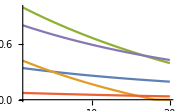

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.85|>];SizePlot[SimulateLawOfMotion[RandomPowerStructure[5]]]
```

#### GenerateReel

Generates a sequence of power structure graph plots (a “reel”) from a simulation. Output: list of graph plots.

```mathematica
GenerateReel[simulation_List]:=Map[ShowPowerStructure,simulation]
```

Same as above, but accepts options for ShowPowerStructure.

```mathematica
GenerateReel[simulation_List,options_Association]:=Map[ShowPowerStructure[#,options]&,simulation]
```

### Monte Carlo

#### ShowMonteCarloSimulation

```mathematica
ShowMonteCarloSimulation[sim_]:=Block[{actors=Join[{0},mctsSimulationActors[sim]]},SpacedRow[MapIndexed[AddCaption[ShowPowerStructure[#,<|"circular"->True,"focal"->actors[[First[#2]]]|>],"t="<>ToString[First[#2]-1]]&,sim],20]
]
```

```mathematica
SetParameters[<|"β"->1.25,"μ"->3,"λ"->.99,"α"->2.05,"δ"->0.3,"ρ"->0.98,"k"->10|>];ShowMonteCarloSimulation[MonteCarloSimulate[ps,3,100,5]]
```

-Graphics-
t=0-Graphics-
t=1-Graphics-
t=2-Graphics-
t=3-Graphics-
t=4-Graphics-
t=5

Given a simulation in which each power structure has a move matrix M, determine which actors caused the power structure to change from one time step to the next. Output: list of list of agent indexes.

```mathematica
mctsSimulationActors[sim_List]:= Block[{ΔTs,Ms},
ΔTs=Differences[Map[ToTernary[#T]&,sim]];
Ms=Map[#M&,Rest[sim]];
MapThread[mctsActors[#1,#2]&,{ΔTs,Ms}]
]
```

```mathematica
mctsSimulationActors[sim]
```

{{4},{1,4},{2,3},{1}}

Determine which actors caused a change in the power structure, given ΔT=T_1 - T_0 (What changed?) and a move matrix M (Who changed it?). This is done by computing ΔT*(M==SymmetrizeT[M]), and then getting the indexes of the nonzero agents.

```mathematica
mctsActors[ΔT_List,M_List]:=Flatten[Position[Abs[Sign[Total[ΔT*MapThread[Boole[Equal[#1,#2]]&,{M,SymmetrizeT[M]},2]]]],1]]
```

```mathematica
mctsActors[({{0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}),({{0, 1, 0, 1, 1}, {1, 0, 1, 1, 1}, {1, 1, 0, 1, 0}, {1, 1, 0, 0, 1}, {1, 0, 0, 1, 0}})]
```

{2,3}

#### MonteCarloShowBestMove

Look at the simultaneous best moves (one time step) based upon MCTS and ReciprocalizeT. Output: two power structure visualizations.

```mathematica
MonteCarloShowBestMove[ps_, depth_,playouts_]:=ShowMonteCarloSimulation[MonteCarloSimulate[ps,depth,playouts,1]]
```

## Unit Tests

### Tests

Master unit test report:

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25, "k"->29|>];report=TestReport[Catenate[{

(* Tactics *)
unitTests["RandomS"],
unitTests["LegalTacticQ"],
unitTests["LegalTacticQ"],
unitTests["LegalTQ"],
unitTests["RandomTactic"],
unitTests["RandomTacticMatrix"],
unitTests["TernaryMatrixQ"],
unitTests["NormalizeS"],
unitTests["NormalizeTactic"],
unitTests["NormalizeTernaryT"],
unitTests["ToTernary"],

(* Simulation Engine *)
unitTests["UpdateS"],
unitTests["SimulateLawOfMotion"],
unitTests["Utility"],
unitTests["PrinceRank"],

(* Visualization *)
unitTests["ShowPowerStructure"],

(* Helper Functions *)
unitTests["HelperFunctions"]
}]]
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.25, "ρ"->0.98|>];
```

TestReportObject[…]

### Analyzing Failures

Shows which test cases failed:

```mathematica
report["TestsFailedWrongResults"]
```

<||>